```mathematica
<<SARAH`
```

Remove::rmptc: Symbol JLink`Fields is Protected and cannot be removed.

SARAH 4.15.3

by Florian Staub, Mark Goodsell and Werner Porod, 2020

contributions by M. Gabelmann, K. Nickel

References:

Comput.Phys.Commun.181 (2010) 1077-1086. (arXiv:0909.2863)

Comput.Phys.Commun.182 (2011) 808-833. (arXiv:1002.0840)

Comput.Phys.Commun.184 (2013) 1792-1809. (arXiv:1207.0906)

Comput.Phys.Commun.185 (2014) 1773-1790. (arXiv:1309.7223)

Eur.Phys.J.C 74 (2014) 8, 2992 (arXiv:1405.1434)

Eur.Phys.J.C 75 (2015) 1, 32 (arXiv:1411.0675)

Eur.Phys.J.C 75 (2015) 6, 290 (arXiv:1503.03098)

Eur.Phys.J.C 77 (2017) 11, 758 (arXiv:1703.09237

Eur.Phys.J.C 77 (2017) 11, 757 (arXiv:1706.05372)

Eur.Phys.J.C 78 (2018) 8, 649 (arXiv:1805.07306)

Download and Documentation:

http://sarah.hepforge.org

Start evaluation of a model with:

Start["Name of Model"]

e.g. Start["MSSM"] or Start["NMSSM","CKM"]

To get a list with all installed models, use ShowModels

```mathematica
Start["SSDM"]
```

Preparing arrays

... checking Directory: /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Models/

Model files loaded

Model    : SSDM

Author(s): Diego Restrepo (based on SM model by F.Staub)

Date     : 2015-11-16

*******************************************************

Loading Susyno functions for the handling of Lie Groups

Based on Susyno v.2.0 by Renato Fonseca (1106.5016)

webpage: web.ist.utl.pt/renato.fonseca/susyno.html

*******************************************************

Initialization

Checking model files:

Initialize gauge groups:

Initialize field:

Preprocessing necessary information:

Checking for anomalies:

Derive Lagrangian

Calculate kinetic Terms

... for scalars: /7 ()

... for fermions: /7 ()

Calculate vector self-interactions: /3 ()

Calculate gauge transformations: /10 ()

Eleminate sums

Calc Complete Lagrangian

Evolve States: GaugeES

Adding terms to the Lagrangian:

... adding: -Yu H.u.q-Yd conj[H].d.q-Ye conj[H].e.l ()

... adding: -1/2 MS2 S.S-mu2 conj[H].H-1/2 LamS S.S.S.S-LamSH S.S.conj[H].H-1/2 Lambda1 conj[H].H.conj[H].H ()

Rotate Lagrangian: /14

Derive ghost terms:

... generate gauge fixing terms: /3 ()

... calculate Ghost interactions

Calc Mixings of Matter Fields

Save information ()

Evolve States: EWSB

Parametrize Higgs Sector

Update gauge transformations: /18 ()

Calc mass matrices gauge sector: /2()

Update gauge transformations: /25 ()

Rotate Lagrangian: /14

Derive ghost terms:

... generate gauge fixing terms: /4 ()

... calculate Ghost interactions

Calc Mixings of Matter Fields

Calculate mass matrices /3 ()

Update gauge transformations: /27 ()

Calculate Tadpole Equations

Save information ()

Finishing

Calculate final Lagrangian

Cleaning up

... add matrix products

... checking for massless particles

... calculating tree level masses ()

... simplify mass matrices

Numerical calculations (if necessary)

... checking for spectrum file:

... reading parameter values and dependences

... calculate mixing matrices

Checking for CP even and odd scalars

All Done. SSDM is ready!

(Model initialized in 9.56357s)

Are you unfamiliar with SARAH? Use SARAH`FirstSteps

```mathematica
Particles[GaugeES]
```

{{VB,1,1,V,{{lorentz,4}}},{gB,1,1,G,{}},{VWB,1,3,V,{{generation,3},{lorentz,4}}},{gWB,1,3,G,{{generation,3}}},{VG,1,1,V,{{color,8},{lorentz,4}}},{gG,1,1,G,{{color,8}}},{H0,1,1,S,{}},{Hp,1,1,S,{}},{ss,1,1,S,{}},{dL,1,3,F,{{generation,3},{color,3}}},{uL,1,3,F,{{generation,3},{color,3}}},{eL,1,3,F,{{generation,3}}},{vL,1,3,F,{{generation,3}}},{dR,1,3,F,{{generation,3},{color,3}}},{uR,1,3,F,{{generation,3},{color,3}}},{eR,1,3,F,{{generation,3}}}}

```mathematica
Masses[GaugeES]
Masses[EWSB]
```

{Mass[VB]→MassGiven[VB],Mass[gB]→MassGiven[gB],Mass[VWB]→MassGiven[VWB],Mass[gWB]→MassGiven[gWB],Mass[VG]→MassGiven[VG],Mass[gG]→MassGiven[gG],Mass[H0]→mu2,Mass[Hp]→mu2}

{Mass[VG]→MassGiven[VG],Mass[gG]→MassGiven[gG],Mass[Hp]→MassGiven[Hp],Mass[ss]→MassRead[ss],Mass[Fv[1]]→MassGiven[Fv[1]],Mass[Fv[2]]→MassGiven[Fv[2]],Mass[Fv[3]]→MassGiven[Fv[3]],Mass[Ah]→MassGiven[Ah],Mass[hh]→MassRead[hh],Mass[VP]→MassGiven[VP],Mass[VZ]→MassGiven[VZ],Mass[gP]→MassGiven[gP],Mass[gZ]→MassGiven[gZ],Mass[gWp]→MassGiven[gWp],Mass[gWpC]→MassGiven[gWpC],Mass[Fd[1]]→MassGiven[Fd[1]],Mass[Fd[2]]→MassGiven[Fd[2]],Mass[Fd[3]]→MassGiven[Fd[3]],Mass[Fd[1]]→MassGiven[Fd[1]],Mass[Fd[2]]→MassGiven[Fd[2]],Mass[Fd[3]]→MassGiven[Fd[3]],Mass[Fu[1]]→MassGiven[Fu[1]],Mass[Fu[2]]→MassGiven[Fu[2]],Mass[Fu[3]]→MassGiven[Fu[3]],Mass[Fu[1]]→MassGiven[Fu[1]],Mass[Fu[2]]→MassGiven[Fu[2]],Mass[Fu[3]]→MassGiven[Fu[3]],Mass[Fe[1]]→MassGiven[Fe[1]],Mass[Fe[2]]→MassGiven[Fe[2]],Mass[Fe[3]]→MassGiven[Fe[3]],Mass[Fe[1]]→MassGiven[Fe[1]],Mass[Fe[2]]→MassGiven[Fe[2]],Mass[Fe[3]]→MassGiven[Fe[3]]}

```mathematica
Lagrangian[GaugeES];
```

```mathematica
ModelOutput[GaugeES,WriteTeX-> True,FeynmanDiagrams->False]
```

Checking model for missing definitions

Transpose::nmtx: The first two levels of {} cannot be transposed.

CheckModelFiles::MissingParticle: The following particle are not defined in ParticleDefinitions in particles.m: {ss}

Transpose::nmtx: The first two levels of {} cannot be transposed.

Generate Directories

Building Particle List

Calculate all vertices

Three Scalar - Interactions

Found 0 potential vertices. Calculating /0)

Four Scalar - Interactions

Found 6 potential vertices. Calculating /6 . ()

Two Scalar - One Vector Boson - Interactions

Found 6 potential vertices. Calculating /6 . ()

Vertex::ChargeViolating: Non-zero result for {Hp,conj[H0],VWB} vertex which violates charge. (This might just be a problem with simplifying the vertex, but could also point towards a mistake in the implementation.)

One Scalar - Two Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Two Scalar - Two Vector Boson - Interactions

Found 10 potential vertices. Calculating /10 . ()

Three Vector Boson - Interactions

Found 2 potential vertices. Calculating /2 . ()

Two Fermion - One Scalar - Interactions

Found 12 potential vertices. Calculating /12 . ()

Two Fermion - One Vector Boson - Interactions

Found 19 potential vertices. Calculating /19 . ()

Four Vector Boson - Interactions

Found 2 potential vertices. Calculating /2 . ()

Two Ghost - One Vector Boson - Interactions

Found 2 potential vertices. Calculating /2 . ()

Two Ghost - One Scalar - Interactions

Two Scalar - One Auxiliary - Interactions

Simplify Vertices

Writing vertices to files

All vertices calculated. (Time needed: 22.3671s)

The vertices are saved in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDM/GaugeES/Vertices/

Generate LaTeX files

Writing Fields and Lagrangian to TeX-File

Writing Particle Content to TeX-File

Write VEVs to TeX-File

Write Flavor Decomposition to TeX-File

Writing Mass Matrices to TeX-File

Writing Tadpole Equations to TeX-File

TeXOutput::NoRGEs: 
 RGEs not calculated so far. Skipping this parts.

Use CalcRGEs[] to calculated RGEs and start MakeTeX again to include them in the output.

TeXOutput::NoLoops: 
 Loop corrections not calculated so far. Skipping this parts.

Use CalcLoopCorrections[States] to calculated RGEs and start MakeTeX again to include them in the output.

Write Clebsch-Gordan Coefficients

Writing Vertices to TeX-File

Done. Output is in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDM/GaugeES/TeX/

Use Script MakePDF.sh (Linux) or MakePDF.bat (Windows) to generate pdf file.

```mathematica
FirstSteps[]
```

Welcome to the SARAH package. SARAH is supposed to give you an easy and quick access to information about supersymmetric and non-supersymmetric models. This includes mass matrices, vertices, renormalisation group equations and one-loop corrections to self-energies and tadpoles. SARAH also creates everything for you that is needed to implement new models in tools like SPheno, WHIZARD/Omega, FeynArts/FormCalc, CalcHep/CompHep and MicrOmegas.

These might be your first steps:

- To generate the entire output for SPheno, WHIZARD, FeynArts, CalcHep and LaTeX, you can use MakeAll[]

- If you have recently created the model, you might check the implementation for consistency using CheckModel

- To take a look at the mass matrices of this model, use MassMatrices[EWSB]

- For an overview about the most important commands use SARAH`Commands

- Run the examples delivered with the package.

If you have any questions or feedback, please send an email to

goodsell@lpthe.jussieu.fr and porod@physik.uni-wuerzburg.de

Null[]

```mathematica
MassMatrices[EWSB]
```

{{{(v Delta[cm1,cn1] Yd[gn1,gm1])/(√2)}},{{-(v Delta[cm1,cn1] Yu[gn1,gm1])/(√2)}},{{(v Ye[gn1,gm1])/(√2)}}}

```mathematica
MakeTeX[]
```

Generate LaTeX files

No Output initialized

Run First ModelOutput[Eigenstates]

No Output created!

```mathematica
ModelOutput[Eigenstates]
```

Checking model for missing definitions

Part::partd: Part specification Particles[Eigenstates]⟦1,4⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

PDG.IX not used, skipping check

Generate Directories

Building Particle List

Part::partd: Part specification Particles[Eigenstates]⟦1,4⟧ is longer than depth of object.

Calculate all vertices

Three Scalar - Interactions

ReplaceAll::reps: {diracSubBack[Eigenstates]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {COUP[diracSubBack[Eigenstates]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Cp[diracSubBack[Eigenstates]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Found 0 potential vertices. Calculating /0)

Four Scalar - Interactions

Found 0 potential vertices. Calculating /0)

Two Scalar - One Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

One Scalar - Two Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Two Scalar - Two Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Three Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Two Fermion - One Scalar - Interactions

Found 0 potential vertices. Calculating /0)

Two Fermion - One Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Four Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Two Ghost - One Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Two Ghost - One Scalar - Interactions

Found 0 potential vertices. Calculating /0)

Two Scalar - One Auxiliary - Interactions

Found 0 potential vertices. Calculating /0)

Simplify Vertices

Writing vertices to files

All vertices calculated. (Time needed: 0.053181s)

The vertices are saved in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDM/Eigenstates/Vertices/

```mathematica
CalcRGEs[TwoLoop->False]
```

Calculate non-supersymmetric RGEs

Initializing Invariants...

Fermion bilinear

(Time needed so far: 1.4857s)

Fermion chains

(Time needed so far: 6.45609s)

Scalar bilinear

... 1-loop

Scalar quartic

... 1-loop

Scalar cubic

... 1-loop

... 2-loop

(Time needed so far: 12.4042s)

All necessary invariants are ready (Time needed: 12.4042s)

Calculation of beta functions...

Calculate Beta Functions for Gauge Couplings

Calculating /3.()

Calculate anomalous dimensions of scalars

Calculating /3.()

Calculate hat(gamma) for running VEVs

Calculating /3.()

Calculate anomalous dimensions of fermions

Calculating /5.()

Calculate Beta Functions for Yukawa-like interactions

Calculating /3.()

Calculate Beta Functions for bilinear Fermion interactions

Nothing to do.

Calculate Beta Functions for scalar 4-point interactions

Calculating /3.()

Calculate Beta Functions for scalar 3-point interactions

Nothing to do.

Calculate Beta Functions for bilinear scalar interactions

Calculating /2.()

Calculate Beta Functions for VEVs

Calculating /1.()

Writing Mathematica code to evaluate RGEs

Finished with the calculation of the RGEs. Time needed: 13.7879s

The results are saved in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDM/RGEs/

```mathematica
sol= RunRGEs[{g1->0.45,g2->0.63,LamSH->1.0},2,5,TwoLoop->False]
```

{{MS2→InterpolatingFunction[…],mu2→InterpolatingFunction[…],v→InterpolatingFunction[…],g1→InterpolatingFunction[…],g2→InterpolatingFunction[…],g3→InterpolatingFunction[…],Yu[1,1]→InterpolatingFunction[…],Yu[2,2]→InterpolatingFunction[…],Yu[3,3]→InterpolatingFunction[…],Yd[1,1]→InterpolatingFunction[…],Yd[2,2]→InterpolatingFunction[…],Yd[3,3]→InterpolatingFunction[…],Ye[1,1]→InterpolatingFunction[…],Ye[2,2]→InterpolatingFunction[…],Ye[3,3]→InterpolatingFunction[…],LamS→InterpolatingFunction[…],LamSH→InterpolatingFunction[…],Lambda1→InterpolatingFunction[…]}}

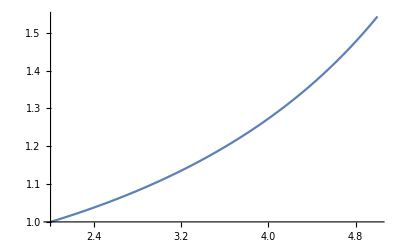

```mathematica
Plot[{LamSH[x]}/.sol[[1]],{x,2,5}]
```

```mathematica
LagSV[EWSB]
```

BosonGaugino-1/2 ⅈ g2 conj[Hp] Delta[1,gen1] Delta[1,gen2] Delta[gen1,gen2] g[lor3,lor4] ((ⅈ Ah Mom[Ah,lor4])/(√2)+(hh Mom[hh,lor4])/(√2)+(v Mom[v,lor4])/(√2)) Sig[i2003,1,2] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2]))-1/2 ⅈ g2 Hp (-(ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] Delta[gen1,gen2] g[lor3,lor4] Mom[Hp,lor4] Sig[i2003,2,1] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2]))+1/2 ⅈ g2 ((ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) conj[Hp] Delta[1,gen1] Delta[1,gen2] Delta[gen1,gen2] g[lor3,lor4] Mom[conj[Hp],lor3] Sig[i2004,1,2] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2]))+1/2 ⅈ g2 Hp Delta[1,gen1] Delta[1,gen2] Delta[gen1,gen2] g[lor3,lor4] (-(ⅈ Ah Mom[Ah,lor3])/(√2)+(hh Mom[hh,lor3])/(√2)+(v Mom[v,lor3])/(√2)) Sig[i2004,2,1] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2]))+1/4 g2^2 (-(ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) ((ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] Delta[gen1,gen5] Delta[gen2,gen5] g[lor3,lor4] Sig[i2003,2,1] Sig[i2004,1,2] sum[i2003,1,3] sum[i2004,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])) (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2]))+1/4 g2^2 Hp conj[Hp] Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] Delta[gen1,gen5] Delta[gen2,gen5] g[lor3,lor4] Sig[i2003,1,2] Sig[i2004,2,1] sum[i2003,1,3] sum[i2004,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])) (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2]))-ⅈ Hp conj[Hp] Delta[1,gen1] Delta[1,gen2] g[lor3,lor4] Mom[Hp,lor4] (1/2 g1 Delta[1,i2003] Delta[gen1,gen2] (Delta[1,gen3] VP[{lor3}] ZZ[1,1]+Delta[1,gen3] VZ[{lor3}] ZZ[1,2])+1/2 g2 Delta[gen1,gen2] Sig[i2003,1,1] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])))+1/2 g2 ((ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) conj[Hp] Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] Delta[gen1,gen5] g[lor3,lor4] Sig[i2004,1,2] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])) (1/2 g1 Delta[1,i2003] Delta[gen2,gen5] (Delta[1,gen3] VP[{lor3}] ZZ[1,1]+Delta[1,gen3] VZ[{lor3}] ZZ[1,2])+1/2 g2 Delta[gen2,gen5] Sig[i2003,1,1] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])))-ⅈ (-(ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] g[lor3,lor4] ((ⅈ Ah Mom[Ah,lor4])/(√2)+(hh Mom[hh,lor4])/(√2)+(v Mom[v,lor4])/(√2)) (1/2 g1 Delta[1,i2003] Delta[gen1,gen2] (Delta[1,gen3] VP[{lor3}] ZZ[1,1]+Delta[1,gen3] VZ[{lor3}] ZZ[1,2])+1/2 g2 Delta[gen1,gen2] Sig[i2003,2,2] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])))+1/2 g2 Hp (-(ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] Delta[gen1,gen5] g[lor3,lor4] Sig[i2004,2,1] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])) (1/2 g1 Delta[1,i2003] Delta[gen2,gen5] (Delta[1,gen3] VP[{lor3}] ZZ[1,1]+Delta[1,gen3] VZ[{lor3}] ZZ[1,2])+1/2 g2 Delta[gen2,gen5] Sig[i2003,2,2] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])))+ⅈ Hp conj[Hp] Delta[1,gen1] Delta[1,gen2] g[lor3,lor4] Mom[conj[Hp],lor3] (1/2 g1 Delta[1,i2004] Delta[gen1,gen2] (Delta[1,gen4] VP[{lor4}] ZZ[1,1]+Delta[1,gen4] VZ[{lor4}] ZZ[1,2])+1/2 g2 Delta[gen1,gen2] Sig[i2004,1,1] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])))+1/2 g2 Hp (-(ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] Delta[gen2,gen5] g[lor3,lor4] Sig[i2003,2,1] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])) (1/2 g1 Delta[1,i2004] Delta[gen1,gen5] (Delta[1,gen4] VP[{lor4}] ZZ[1,1]+Delta[1,gen4] VZ[{lor4}] ZZ[1,2])+1/2 g2 Delta[gen1,gen5] Sig[i2004,1,1] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])))+Hp conj[Hp] Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] g[lor3,lor4] (1/2 g1 Delta[1,i2003] Delta[gen2,gen5] (Delta[1,gen3] VP[{lor3}] ZZ[1,1]+Delta[1,gen3] VZ[{lor3}] ZZ[1,2])+1/2 g2 Delta[gen2,gen5] Sig[i2003,1,1] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2]))) (1/2 g1 Delta[1,i2004] Delta[gen1,gen5] (Delta[1,gen4] VP[{lor4}] ZZ[1,1]+Delta[1,gen4] VZ[{lor4}] ZZ[1,2])+1/2 g2 Delta[gen1,gen5] Sig[i2004,1,1] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])))+ⅈ ((ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] g[lor3,lor4] (-(ⅈ Ah Mom[Ah,lor3])/(√2)+(hh Mom[hh,lor3])/(√2)+(v Mom[v,lor3])/(√2)) (1/2 g1 Delta[1,i2004] Delta[gen1,gen2] (Delta[1,gen4] VP[{lor4}] ZZ[1,1]+Delta[1,gen4] VZ[{lor4}] ZZ[1,2])+1/2 g2 Delta[gen1,gen2] Sig[i2004,2,2] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])))+1/2 g2 ((ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) conj[Hp] Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] Delta[gen2,gen5] g[lor3,lor4] Sig[i2003,1,2] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2])) (1/2 g1 Delta[1,i2004] Delta[gen1,gen5] (Delta[1,gen4] VP[{lor4}] ZZ[1,1]+Delta[1,gen4] VZ[{lor4}] ZZ[1,2])+1/2 g2 Delta[gen1,gen5] Sig[i2004,2,2] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])))+(-(ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) ((ⅈ Ah)/(√2)+hh/(√2)+v/(√2)) Delta[1,gen1] Delta[1,gen2] Delta[1,gen5] g[lor3,lor4] (1/2 g1 Delta[1,i2003] Delta[gen2,gen5] (Delta[1,gen3] VP[{lor3}] ZZ[1,1]+Delta[1,gen3] VZ[{lor3}] ZZ[1,2])+1/2 g2 Delta[gen2,gen5] Sig[i2003,2,2] sum[i2003,1,3] (Delta[1,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[1,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[1,2])+Delta[2,i2003] (Delta[1,gen3] VWp[{lor3}] ZW[2,1]+conj[VWp[{lor3}]] Delta[1,gen3] ZW[2,2])+Delta[3,i2003] (Delta[1,gen3] VP[{lor3}] ZZ[2,1]+Delta[1,gen3] VZ[{lor3}] ZZ[2,2]))) (1/2 g1 Delta[1,i2004] Delta[gen1,gen5] (Delta[1,gen4] VP[{lor4}] ZZ[1,1]+Delta[1,gen4] VZ[{lor4}] ZZ[1,2])+1/2 g2 Delta[gen1,gen5] Sig[i2004,2,2] sum[i2004,1,3] (Delta[1,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[1,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[1,2])+Delta[2,i2004] (Delta[1,gen4] VWp[{lor4}] ZW[2,1]+conj[VWp[{lor4}]] Delta[1,gen4] ZW[2,2])+Delta[3,i2004] (Delta[1,gen4] VP[{lor4}] ZZ[2,1]+Delta[1,gen4] VZ[{lor4}] ZZ[2,2])))